### Part 1a

```mathematica
μe =398600.4418 ;
μm=4902.8;
am =384400.;
asc =am/(3/4)^(2/3)(*check this it could be the inverse*)
e =0.75;
rp =asc(1-e);
vp = Sqrt[μe ((1+e)/(asc(1-e)))];
tm = 2π Sqrt[am^3/μe];
tsc =tm (asc/am)^(3/2);
nm = √(μe/am^3);
tu=tm/(2 Pi);
μ=0.0121504632;
```

465667.

```mathematica
tsctu =tsc/tu;
```

```mathematica
transfer=NDSolve[{x''[t]==-μe/((x[t]^2+y[t]^2)^(3/2))x[t],y''[t]==-μe/((x[t]^2+y[t]^2)^(3/2))y[t],x[0]==rp,y[0]==0,x'[0]==0,y'[0]==vp},{x,y},{t,0,tsc}][[1]];
xm[t_]:= am Cos[nm t]
ym[t_]:= am Sin[nm t]
```

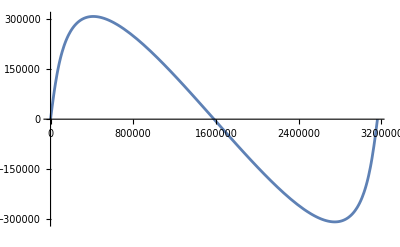

```mathematica
Plot[y[t]/.transfer,{t,0,tsc}]
```

### Part 1b

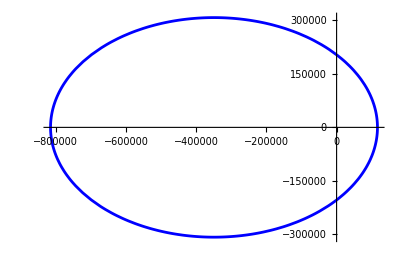

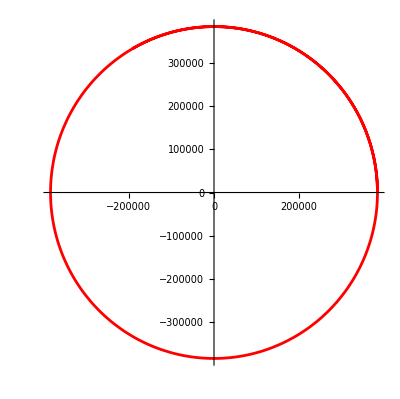

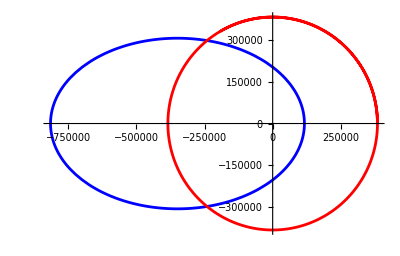

```mathematica
spcorb=ParametricPlot[{x[t],y[t]}/. transfer,{t,0,tsc},PlotRange->All,PlotStyle->Blue,PlotLegends->"Sc"]

moonorb=ParametricPlot[{xm[t],ym[t]}/. transfer,{t,0,tsc},PlotRange->All,PlotStyle->Red]

Show[{spcorb,moonorb},PlotLegends->{"Spacecraft","Moon"}]
```

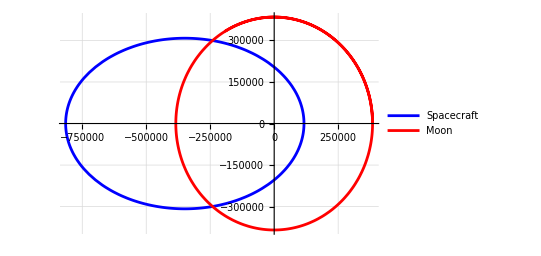

```mathematica
ParametricPlot[Evaluate[{{x[t],y[t]}/. transfer,{xm[t],ym[t]}/. transfer}],{t,0,tsc},PlotRange->All,PlotStyle->{Blue,Red},PlotLegends->Placed[{"Spacecraft","Moon"},Right],AxesOrigin->{0,0},GridLines->Automatic]
```

```mathematica
rECI0={rp,0,0};
vECI0={0,vp,0};
```

### Part 1c

```mathematica
rcm[t_]:=μ/am{xm[t],ym[t],0};
vcm[t_]:=Evaluate[rcm'[t]]
```

```mathematica
ECItoCR3BP[r_,v_,t_]:=Module[{DU,TM,TU,θ,R,rN,vN,rSyn,vSyn,ω,rcmN,vcmN},DU=384400;
TM=2π Sqrt[am^3/μe];
TU=TM/(2 Pi);
vcmN=vcm[t]/(DU/TU);
rcmN = rcm[t]/DU;
rN=r/DU;
vN=v/(DU/TU);
θ=t/TU;
R={{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}};
rSyn=R.(rN-rcmN);
ω={0,0,1};
vSyn=R.(vN-vcmN)-Cross[ω,rSyn];
{rSyn,vSyn}]
```

```mathematica
x'[0]/. transfer(* x'[0]==0 check the nd solve*)
```

5.6832×10^-25

```mathematica
y'[0]/. transfer
```

2.44782

### Part 1d

```mathematica
{r0Syn,v0Syn} = ECItoCR3BP[rECI0,vECI0,0];
x0Syn=r0Syn[[1]];
y0Syn=r0Syn[[2]];
vx0Syn=v0Syn[[1]];
vy0Syn=v0Syn[[2]];
```

```mathematica
ic = {x[0]==x0Syn ,y[0]==y0Syn,x'[0]==vx0Syn,y'[0]==vy0Syn};
eqns={x''[t]-2 y'[t]==x[t]-((1-μ)*(x[t]+μ))/r1[t]^3-(μ*(x[t]+μ-1))/r2[t]^3,y''[t]+2 x'[t]==y[t]-((1-μ)*y[t])/r1[t]^3-(μ*y[t])/r2[t]^3,r1[t]==Sqrt[(x[t]+μ)^2+y[t]^2],r2[t]==Sqrt[(x[t]-(1-μ))^2+y[t]^2]};
```

```mathematica
solCR3BP=NDSolve[Join[eqns,ic],{x,y},{t,0,2 π}];
```

```mathematica
solCR3BP
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
{-μ,0},{1-μ,0}
```

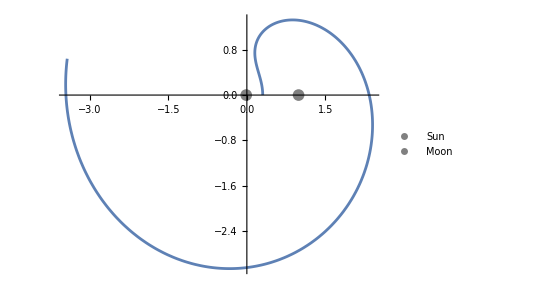

```mathematica
Show[ParametricPlot[{x[t],y[t]}/. solCR3BP,{t,0,2 Pi}],ListPlot[{Legended[{-μ,0},"Sun"],Legended[{1-μ,0},"Moon"]},PlotStyle->{Yellow,Gray},PlotMarkers->{{"●",12},{"●",12}}]]
```

### Part e

```mathematica
F[x_,y_,vx_,vy_]:={x-((1-μ)*(x+μ))/r1[x,y]^3-(μ*(x+μ-1))/r2[x,y]^3+2 vy,-2 vx+y-((1-μ)*y)/r1[x,y]^3-(μ*y)/r2[x,y]^3}
r1[x_,y_]:=Sqrt[(x+μ)^2+y^2];
r2[x_,y_]:=Sqrt[(x-(1-μ))^2+y^2]
```

```mathematica
trajectory=ParametricNDSolve[{x''[t]==F[x[t],y[t],x'[t],y'[t]][[1]] ,y''[t]==F[x[t],y[t],x'[t],y'[t]][[2]],x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,2 π},{x0,y0,vx0,vy0}];
```

```mathematica
f[x_,y_,vx_,vy_]:= {vx,vy,F[x,y,vx,vy]}//Flatten
αs={x,y,vx,vy};
A[x_,y_,vx_,vy_]:=Evaluate[Table[D[f[x,y,vx,vy][[i]],α],{i,1,4},{α,αs}](*/.{Abs'[z_]Abs[z_]->z}*)]
Φ=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"[t]"],{i,4},{j,4}];
Φ0=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"[0]"],{i,4},{j,4}];
dΦdt=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"'[t]"],{i,4},{j,4}];
unknowns =Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]],{i,4},{j,4}]//Flatten;
stmeq[x0_,y0_,vx0_,vy0_]:=(#==0)&/@Flatten[dΦdt-(A[x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t],x[x0,y0,vx0,vy0]'[t],y[x0,y0,vx0,vy0]'[t]]/.trajectory).Φ]
stmic = (#==0)&/@Flatten[Φ0-IdentityMatrix[4]];
stmfull[x0_,y0_,vx0_,vy0_]:=Join[stmeq[x0,y0,vx0,vy0],stmic]
```

```mathematica
stm[x0_?NumericQ,y0_?NumericQ,vx0_?NumericQ,vy0_?NumericQ,tf_?NumericQ]:=ArrayReshape[Through[NDSolve[stmfull[x0,y0,vx0,vy0],unknowns,{t,0,tf}][[1]][[All,2]][tf]],{4,4}]
```

```mathematica
stm[x0Syn,y0Syn,vx0Syn,vy0Syn,3]//MatrixForm
```

(21.4453 | -1.87822 | -0.684711 | 4.53357
-43.9383 | -6.55964 | -2.12646 | -8.21157
-27.0797 | -6.37121 | -2.0517 | -4.9432
-36.7292 | 0.454596 | 0.221473 | -7.53421)

```mathematica
error[{vy0_,tf_}]:= { y[x0Syn, 0 , 0,vy0 ][tf] -0,x[x0Syn, 0 , 0,vy0]'[tf]-0 }/.trajectory
```

```mathematica
error[{vy0Syn,π}]
```

{-1.07835,-0.556138}

```mathematica
Sensm[x0_,y0_,vx0_,vy0_,t_]:={{stm[x0,y0,vx0,vy0,t][[2,4]],y[x0Syn, 0 , 0,vy0]'[t] },{stm[x0,y0,vx0,vy0,t][[3,4]], x[x0Syn, 0 , 0,vy0]''[t]}}/.trajectory
```

```mathematica
invsensm[{vy0_,tf_}]:= Inverse[Sensm[x0Syn,y0Syn,vx0Syn,vy0,tf]]
```

```mathematica
n=100;
param = 0.1;
XState=ConstantArray[0,n];
ERR=ConstantArray[0,n];
B=ConstantArray[0,n];
XState[[1]] = {vy0Syn,tsctu/2};
ERR[[1]]=error[XState[[1]]];
B[[1]]=invsensm[XState[[1]]];
Dynamic[i]
```

```mathematica
For[i=1,i<n,i++,
XState[[i+1]]=XState[[i]]-param (B[[i]].ERR[[i]]);
ERR[[i+1]]=error[XState[[i+1]]];
B[[i+1]]=invsensm[XState[[i+1]]];
]
```

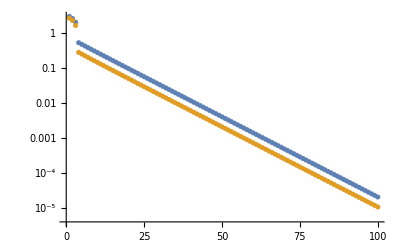

```mathematica
ListLogPlot[ERR//Transpose//Abs]
```

```mathematica
XState[[-1]]- {vy0Syn,tsctu}
```

{-0.109577,-5.26628}

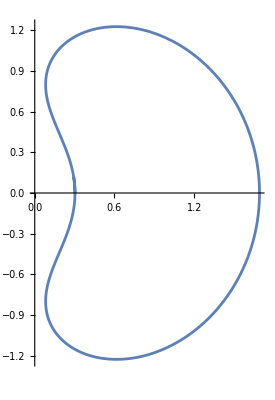

```mathematica
closed=ParametricPlot[{x[x0Syn,y0Syn,vx0Syn,XState[[-1]][[1]]][t],y[x0Syn,y0Syn,vx0Syn,XState[[-1]][[1]]][t]}/.trajectory,{t,0,2π}]
```

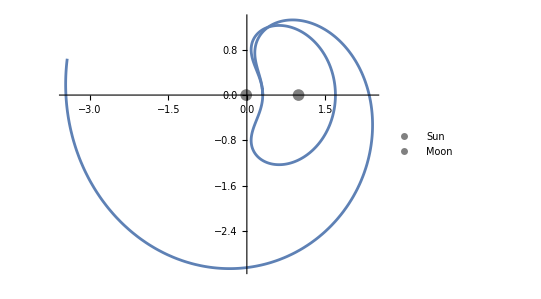

```mathematica
Show[ParametricPlot[{x[t],y[t]}/. solCR3BP,{t,0,2 Pi}],ListPlot[{Legended[{-μ,0},"Sun"],Legended[{1-μ,0},"Moon"]},PlotStyle->{Yellow,Gray},PlotMarkers->{{"●",12},{"●",12}}],closed]
```